# Position projections

## Definitions

## DTQW Environment

```mathematica
$DTQWEnvIcon=Graphics[{
Thick,
Circle[],
PointSize[Large],
Point[{0,0}]
},
ImageSize->Dynamic[{
Automatic,
3.5 CurrentValue["FontCapHeight"]/AbsoluteCurrentValue[Magnification]
}]
];
```

```mathematica
DTQWEnvAscQ[asc_?AssociationQ]:=And[
AllTrue[{"Type","Decoherent"},KeyExistsQ[asc,#]&],
Or[KeyExistsQ[asc,"Unitary"],AllTrue[{"Shift","Coin"},KeyExistsQ[asc,#]&]],
Xnor[asc["Decoherent"],AllTrue[{"Kraus","Probabilities"},KeyExistsQ[asc,#]&]],
Xnor[asc["Type"]=="FixedSize",KeyExistsQ[asc,"Size"]]
]
```

```mathematica
DTQWEnv[asc_?DTQWEnvAscQ]:=Module[{shift,coin,unit},
shift=asc["Shift"];
coin=asc["Coin"];
unit=Function[n,shift[n].coin[n]];
DTQWEnv[Append[asc,"Unitary"->unit]]
]/;Not[KeyExistsQ[asc,"Unitary"]]
```

```mathematica
DTQWEnv/:MakeBoxes[obj:DTQWEnv[asc_?DTQWEnvAscQ],form:(StandardForm|TraditionalForm)]:=
Module[{above,below},
above={
{BoxForm`SummaryItem[{"Type: ",asc["Type"]}],SpanFromLeft},
{BoxForm`SummaryItem[{"Decoherent: ",asc["Decoherent"]}],BoxForm`SummaryItem[{"Size: ",If[KeyExistsQ[asc,"Size"],asc["Size"],{∞,2}]}]}
};
below={
{BoxForm`SummaryItem[{"Information: ","This object represents a 1-dimensional discrete-time quantum walk with a two-dimensional coin"}],SpanFromLeft}
};
BoxForm`ArrangeSummaryBox[
DTQWEnv,
obj,
$DTQWEnvIcon,
above,
below,
form,
"Interpretable"->Automatic
]
];
```

## Spacing function

```mathematica
DTQWSpacing[rho_,"ForwardGrowing"]:=ArrayPad[rho,{{0,2},{0,2}}]
DTQWSpacing[rho_,"Growing"]:=ArrayPad[rho,2]
DTQWSpacing[rho_,"FixedSize"]:=rho
DTQWSpacing[rho_,s_String]:=With[{n=Read[StringToStream[StringDrop[s,-5]],Number]},
ArrayPad[rho,{{0,2*n},{0,2*n}}]
]/;(StringTake[s,-5]=="Ahead")
DTQWSpacing[rho_,"Both"]:=ArrayPad[rho,2]
```

## DTQW step

```mathematica
DTQWStep[rho_,DTQWEnv[env_]]:=With[{
bigrho=DTQWSpacing[rho,env["Type"]]
},
Chop[ApplyOperator[#,bigrho]]&[env["Unitary"][Length[bigrho]/2]]/;Not[env["Decoherent"]]
]
DTQWStep[rho_,DTQWEnv[env_]]:=Module[{
bigrho=DTQWSpacing[rho,env["Type"]],
state
},
state=ApplyOperator[#,bigrho]&[env["Unitary"][Length[bigrho]/2]];
Inner[Chop[#1*ApplyOperator[#2[Length[bigrho]/2],state]]&,env["Probabilities"],env["Kraus"],Plus]
]
```

## DTQW

```mathematica
DTQW[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Do[ρ=DTQWStep[ρ,env],{t,n}];
ρ
]
DTQW[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Do[ρ=DTQWStep[ρ,env],{t,n}];
ρ
]/;(env[[1]]["Type"]=="TwoAhead")
DTQW[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Do[ρ=DTQWStep[ρ,env],{t,n}];
ρ
]/;(env[[1]]["Type"]=="Two")
```

## DTQW Trace

```mathematica
DTQWTrace[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Table[ρ=DTQWStep[ρ,env],{t,n}]
]
DTQWTrace[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Table[ρ=DTQWStep[ρ,env],{t,n}]
]/;(env[[1]]["Type"]=="TwoAhead")
DTQWTrace[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Table[ρ=DTQWStep[ρ,env],{t,n}]
]/;(env[[1]]["Type"]=="Two")
```

## DTQWQuanticity

```mathematica
DTQWQuanticity[coin_,range_]:=Module[{env,probs,sds,lm,nlm,p},
Table[
env=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{1-p,p},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,PositionprojOperator}
|>];
probs=DTQWPosDistribution/@DTQWTrace[coin,100,env];
sds=DTQWPosStandardev/@probs;
lm=LinearModelFit[sds,x,x];
nlm=NonlinearModelFit[sds,A*Sqrt[x],{A},x];
{p,lm["AdjustedRSquared"],nlm["AdjustedRSquared"]},
{p,range}
]
]
(* Función incompleta, falta añadir funcionalidad usando la función para modificar envs *)
```

## Misc. functions

```mathematica
ApplyOperator[operator_?MatrixQ,rho_]:=operator.rho.ConjugateTranspose[operator]
ApplyOperator[operator_Function,rho_]:=operator[rho]
```

```mathematica
DTQWPosDistribution[rho_]:=Total/@Partition[Diagonal@rho,2]
```

```mathematica
DTQWPosExpvalue[prob_]:=Range[Length[#]].#&[prob]
```

```mathematica
DTQWPosStandardev[prob_]:=Sqrt[(Range[Length[#]]^2).#-DTQWPosExpvalue[#]^2]&[prob]
```

```mathematica
DTQWSdAdjustments[stdev_]:=Module[{lm,nlm},
lm=NonlinearModelFit[stdev,A*x,{A},x];
nlm=NonlinearModelFit[stdev,A*Sqrt[x],{A},x];
If[lm["AdjustedRSquared"]<nlm["AdjustedRSquared"],
nlm,
lm
]
](* Revisar función luego *)
```

```mathematica
DTQWSummary[coin_,n_,env_]:=Module[{steps,probs,sds,adjst},
steps=DTQWTrace[coin,n,env];
probs=DTQWPosDistribution/@steps;
sds=DTQWPosStandardev/@probs;
adjst=DTQWSdAdjustments[sds];
GraphicsRow[{
ListLinePlot[probs[[-1]],
PlotLabel->"DTQW",
PlotRange->All,
Mesh->All
],
ListPlot[sds,
PlotLabel->adjst["BestFit"],
PlotRange->All
]
}]
]
DTQWSummary[coin_,env_]:=Module[{steps,probs,sds,adjst},
steps=DTQWTrace[coin,100,env];
probs=DTQWPosDistribution/@steps;
sds=DTQWPosStandardev/@probs;
adjst=DTQWSdAdjustments[sds];
GraphicsRow[{
ListLinePlot[probs[[-1]],
PlotLabel->"DTQW",
PlotRange->All,
Mesh->All
],
ListPlot[sds,
PlotLabel->adjst["BestFit"],
PlotRange->All
]
}]
]
```

## DTQW Matrix Plot

```mathematica
DTQWMatrixPlot[c0_,n_,env_,h_]:=Module[{dmats},
dmats=MatrixPartialTrace[#,h,{Round[Length[#]/2],2}]&/@DTQWTrace[c0,n,env];
ArrayPlot[#,
PlotLegends->Automatic,
ColorFunction->(Blend[{White,Blend[{Purple,Black},0.3]},#]&),
Mesh->True,
MeshStyle->Black
]&/@Table[m,{m,Abs[dmats]}]
]
```

## DTQW Equation Print

```mathematica
DTQWEquationPrint[probs_,kraus_]:=With[{tex="\\mathcal{E}(\\rho) = "<>Fold[#1<>"+"<>#2&,MapThread[#1<>""<>#2[[1]]<>"U \\rho U^\\dagger "<>#2[[2]]&,{probs,Map[If[""==#,{"",""},{#,#<>"^\\dagger "}]&,kraus]}]]},
URLExecute["https://math.vercel.app/",{"bgcolor"->"auto","from"->"\\LARGE "<>ToString[tex]<>".svg"}]//Style[#,TextAlignment->Center]&
]
```

## External stuff

```mathematica
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
```

## Examples

## Operadores

```mathematica
α=π/6.;
CoinOperator[n_]:=SparseArray[Band[{1,1},{#,#}]->{{{Cos[α],Sin[α]},{-Sin[α],Cos[α]}}}]&[2n]
ShiftOperator[n_]:=SparseArray[Join[Table[{i,i},{i,Range[2,#,2]}],Table[{i,i-2},{i,Range[3,#,2]}]]->1,{#,#}]&[2*n]
UnitaryOperator[n_]:=ShiftOperator[n].CoinOperator[n]
PositionprojOperator[n_]:=Function[rho,DiagonalMatrix@Diagonal[rho]]
FuzzyOperator[n_]:=RotateRight[IdentityMatrix[2*n,SparseArray],2]
PermutationOperators[s_]:=Function[n,RotateRight[IdentityMatrix[2*n,SparseArray],2*s]]
```

## Cálculos

```mathematica
coin={1,ⅈ}/Sqrt[2.];
```

### Animación 3 pasos

#### Decoherencia con shift y coin

```mathematica
env3D=DTQWEnv[<|
"Type"->(ToString[#]<>"Ahead"),"Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->N[{0.5}~Join~ConstantArray[1/(2(#-1)),#-1]],
"Kraus"->(PermutationOperators/@Range[0,#-1])
|>]&@3;
```

```mathematica
steps3D=DTQWTrace[coin,100,env3D];
probs3D=DTQWPosDistribution/@steps3D;
sds3D=DTQWPosStandardev/@probs3D;
ln3D=NonlinearModelFit[sds3D,A*x,{A},x];
sq3D=NonlinearModelFit[sds3D,A*Sqrt[x],{A},x];
```

#### Decoherencia con shift y sin moneda

```mathematica
env3D1=DTQWEnv[<|
"Type"->(ToString[#]<>"Ahead"),"Decoherent"->True,"Unitary"->(ShiftOperator[#].IdentityMatrix[2*#,SparseArray]&),
"Probabilities"->N[{0.5}~Join~ConstantArray[1/(2(#-1)),#-1]],
"Kraus"->(PermutationOperators/@Range[0,#-1])
|>]&@3;
```

```mathematica
steps3D1=DTQWTrace[coin,100,env3D1];
probs3D1=DTQWPosDistribution/@steps3D1;
sds3D1=DTQWPosStandardev/@probs3D1;
ln3D1=NonlinearModelFit[sds3D1,A*x,{A},x];
sq3D1=NonlinearModelFit[sds3D1,A*Sqrt[x],{A},x];
```

#### Decoherencia sin shift ni moneda

```mathematica
env3D2=DTQWEnv[<|
"Type"->(ToString[#]<>"Ahead"),"Decoherent"->True,"Unitary"->(IdentityMatrix[2*#,SparseArray]&),
"Probabilities"->N[{0.5}~Join~ConstantArray[1/(2(#-1)),#-1]],
"Kraus"->(PermutationOperators/@Range[0,#-1])
|>]&@3;
```

```mathematica
steps3D2=DTQWTrace[coin,100,env3D2];
probs3D2=DTQWPosDistribution/@steps3D2;
sds3D2=DTQWPosStandardev/@probs3D2;
ln3D2=NonlinearModelFit[sds3D2,A*x,{A},x];
sq3D2=NonlinearModelFit[sds3D2,A*Sqrt[x],{A},x];
```

#### Animación dist. de probabilidad

```mathematica
Manipulate[
ListLinePlot[{probs3D[[i]],probs3D1[[i]],probs3D2[[i]]},
PlotRange->All,
Mesh->All,
PlotLegends->{"3 Dsc","3 Ds","3 D"}
],{i,1,Length[probs3D],1}
]
```

#### Animación desv. estándar

```mathematica
Manipulate[
Show[{
Plot[{ln3D[x],ln3D1[x],ln3D2[x]}[[i]],{x,0,200},
PlotStyle->Dashed,
PlotLabel->({"Dsc","Ds","D"}[[i]])
],
Plot[{sq3D[x],sq3D1[x],sq3D2[x]}[[i]],{x,0,200},
PlotStyle->Dotted
],
ListLinePlot[{sds3D,sds3D1,sds3D2}[[i]]]
}],
{i,1,3,1}
]
```

```mathematica
Manipulate[
Show[{
Plot[{lnD[x],lnD1[x],lnD2[x]}[[i]],{x,0,200},
PlotStyle->Dashed,
PlotLabel->({"Dsc","Ds","D"}[[i]])
],
Plot[{sqD[x],sqD1[x],sqD2[x]}[[i]],{x,0,200},
PlotStyle->Dotted
],
ListLinePlot[{sdsD,sdsD1,sdsD2}[[i]]]
}],
{i,1,3,1}
]
```

### Animación 10 pasos

#### Decoherencia con shift y coin

```mathematica
env10D=DTQWEnv[<|
"Type"->(ToString[#]<>"Ahead"),"Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->N[{0.5}~Join~ConstantArray[1/(2(#-1)),#-1]],
"Kraus"->(PermutationOperators/@Range[0,#-1])
|>]&@10;
```

```mathematica
steps10D=DTQWTrace[coin,100,env10D];
probs10D=DTQWPosDistribution/@steps10D;
sds10D=DTQWPosStandardev/@probs10D;
ln10D=NonlinearModelFit[sds10D,A*x,{A},x];
sq10D=NonlinearModelFit[sds10D,A*Sqrt[x],{A},x];
```

#### Decoherencia con shift y sin moneda

```mathematica
env10D1=DTQWEnv[<|
"Type"->(ToString[#]<>"Ahead"),"Decoherent"->True,"Unitary"->(ShiftOperator[#].IdentityMatrix[2*#,SparseArray]&),
"Probabilities"->N[{0.5}~Join~ConstantArray[1/(2(#-1)),#-1]],
"Kraus"->(PermutationOperators/@Range[0,#-1])
|>]&@10;
```

```mathematica
steps10D1=DTQWTrace[coin,100,env10D1];
probs10D1=DTQWPosDistribution/@steps10D1;
sds10D1=DTQWPosStandardev/@probs10D1;
ln10D1=NonlinearModelFit[sds10D1,A*x,{A},x];
sq10D1=NonlinearModelFit[sds10D1,A*Sqrt[x],{A},x];
```

#### Decoherencia sin shift ni moneda

```mathematica
env10D2=DTQWEnv[<|
"Type"->(ToString[#]<>"Ahead"),"Decoherent"->True,"Unitary"->(IdentityMatrix[2*#,SparseArray]&),
"Probabilities"->N[{0.5}~Join~ConstantArray[1/(2(#-1)),#-1]],
"Kraus"->(PermutationOperators/@Range[0,#-1])
|>]&@10;
```

```mathematica
steps10D2=DTQWTrace[coin,100,env10D2];
probs10D2=DTQWPosDistribution/@steps10D2;
sds10D2=DTQWPosStandardev/@probs10D2;
ln10D2=NonlinearModelFit[sds10D2,A*x,{A},x];
sq10D2=NonlinearModelFit[sds10D2,A*Sqrt[x],{A},x];
```

#### Animación dist. de probabilidad

```mathematica
Manipulate[
ListLinePlot[{probs10D[[i]],probs10D1[[i]],probs10D2[[i]]},
PlotRange->All,
Mesh->All,
PlotLegends->{"10 Dsc","10 Ds","10 D"}
],{i,1,Length[probs10D],1}
]
```

#### Animación desv. estándar

```mathematica
Manipulate[
Show[{
Plot[{ln10D[x],ln10D1[x],ln10D2[x]}[[i]],{x,0,200},
PlotStyle->Dashed,
PlotLabel->({"Dsc","Ds","D"}[[i]])
],
Plot[{sq10D[x],sq10D1[x],sq10D2[x]}[[i]],{x,0,200},
PlotStyle->Dotted
],
ListLinePlot[{sds10D,sds10D1,sds10D2}[[i]]]
}],
{i,1,3,1}
]
```

```mathematica
Manipulate[
Show[{
Plot[{lnD[x],lnD1[x],lnD2[x]}[[i]],{x,0,200},
PlotStyle->Dashed,
PlotLabel->({"Dsc","Ds","D"}[[i]])
],
Plot[{sqD[x],sqD1[x],sqD2[x]}[[i]],{x,0,200},
PlotStyle->Dotted
],
ListLinePlot[{sdsD,sdsD1,sdsD2}[[i]]]
}],
{i,1,3,1}
]
```

### Probabilidad equidistribuida

#### 1 paso adicional

```mathematica
env02=DTQWEnv[<|
"Type"->(ToString[#]<>"Ahead"),"Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->N[ConstantArray[1/#,#]],
"Kraus"->(PermutationOperators/@Range[0,#-1])
|>]&@2;
```

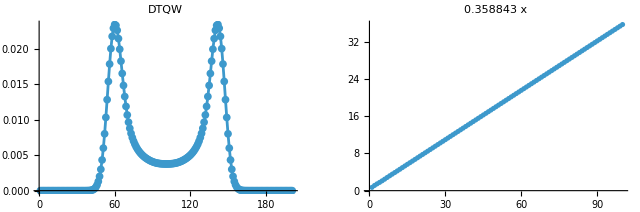

```mathematica
DTQWSummary[coin,env02]
```

#### 8 pasos adicionales

```mathematica
env09=DTQWEnv[<|
"Type"->(ToString[#]<>"Ahead"),"Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->N[ConstantArray[1/#,#]],
"Kraus"->(PermutationOperators/@Range[0,#-1])
|>]&@9;
```

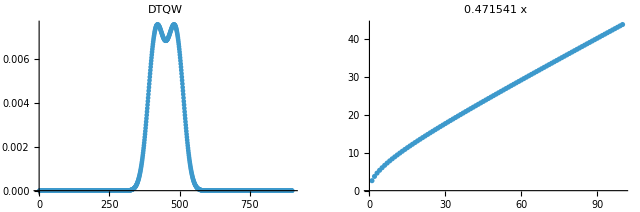

```mathematica
DTQWSummary[coin,env09]
```

#### 9 pasos adicionales

```mathematica
env10=DTQWEnv[<|
"Type"->(ToString[#]<>"Ahead"),"Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->N[ConstantArray[1/#,#]],
"Kraus"->(PermutationOperators/@Range[0,#-1])
|>]&@10;
```

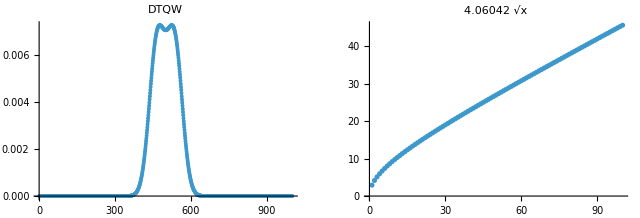

```mathematica
DTQWSummary[coin,env10]
```

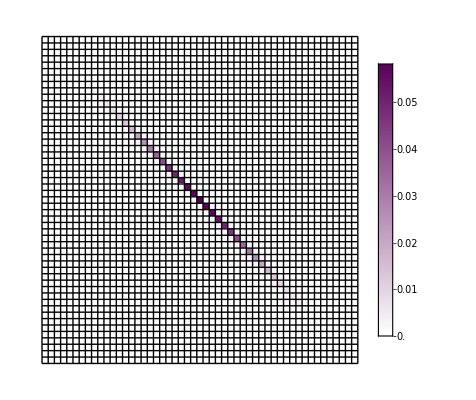

```mathematica
ArrayPlot[Abs[MatrixPartialTrace[#,2,{Length[#]/2,2}]&@DTQW[coin,5,env10]],
PlotLegends->Automatic,
ColorFunction->(Blend[{White,Blend[{Purple,Black},0.3]},#]&),
Mesh->True,
MeshStyle->Black
]
```

### Probabilidad sobreestimada

#### 9 pasos adicionales

```mathematica
envT=DTQWEnv[<|
"Type"->(ToString[#]<>"Ahead"),"Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->N[{0.5}~Join~ConstantArray[1/(2(#-1)),#-1]],
"Kraus"->(PermutationOperators/@Range[0,#-1])
|>]&@10;
```

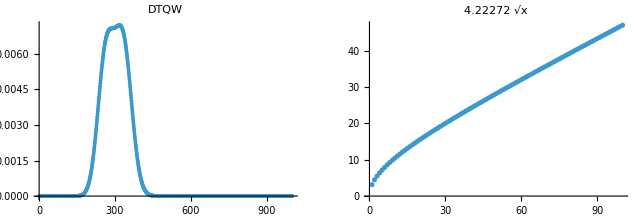

```mathematica
DTQWSummary[coin,envT]
```

## More steps

### 8 pasos (100)

```mathematica
envT=DTQWEnv[<|
"Type"->(ToString[#]<>"Ahead"),"Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->N[{0.5}~Join~ConstantArray[1/(2(#-1)),#-1]],
"Kraus"->(PermutationOperators/@Range[0,#-1])
|>]&@9;
```

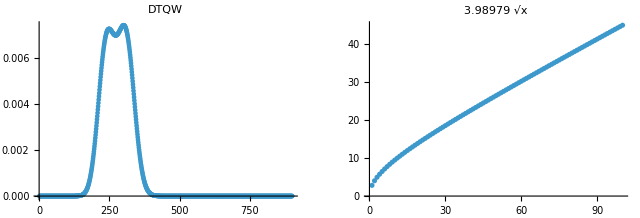

```mathematica
DTQWSummary[coin,100,envT]
```

### 8 pasos

```mathematica
envT=DTQWEnv[<|
"Type"->(ToString[#]<>"Ahead"),"Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->N[{0.5}~Join~ConstantArray[1/(2(#-1)),#-1]],
"Kraus"->(PermutationOperators/@Range[0,#-1])
|>]&@9;
```

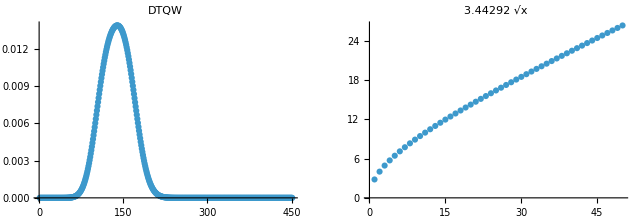

```mathematica
DTQWSummary[coin,50,envT]
```

### 7 pasos

```mathematica
envT1=DTQWEnv[<|
"Type"->(ToString[#]<>"Ahead"),"Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->N[{0.5}~Join~ConstantArray[1/(2(#-1)),#-1]],
"Kraus"->(PermutationOperators/@Range[0,#-1])
|>]&@8;
```

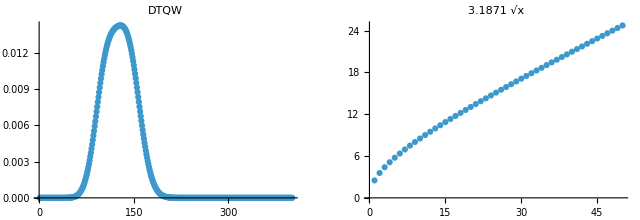

```mathematica
DTQWSummary[coin,50,envT1]
```

### 6 pasos

```mathematica
envT2=DTQWEnv[<|
"Type"->(ToString[#]<>"Ahead"),"Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->N[{0.5}~Join~ConstantArray[1/(2(#-1)),#-1]],
"Kraus"->(PermutationOperators/@Range[0,#-1])
|>]&@7;
```

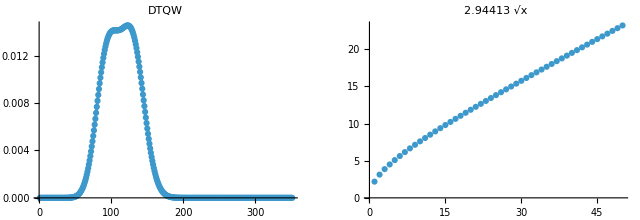

```mathematica
DTQWSummary[coin,50,envT2]
```

### 5 pasos

```mathematica
envT3=DTQWEnv[<|
"Type"->(ToString[#]<>"Ahead"),"Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->N[{0.5}~Join~ConstantArray[1/(2(#-1)),#-1]],
"Kraus"->(PermutationOperators/@Range[0,#-1])
|>]&@6;
```

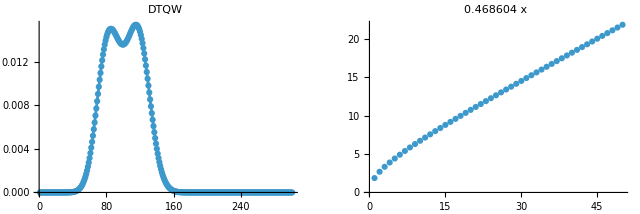

```mathematica
DTQWSummary[coin,50,envT3]
```

### 4 pasos

```mathematica
envT4=DTQWEnv[<|
"Type"->(ToString[#]<>"Ahead"),"Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->N[{0.5}~Join~ConstantArray[1/(2(#-1)),#-1]],
"Kraus"->(PermutationOperators/@Range[0,#-1])
|>]&@5;
```

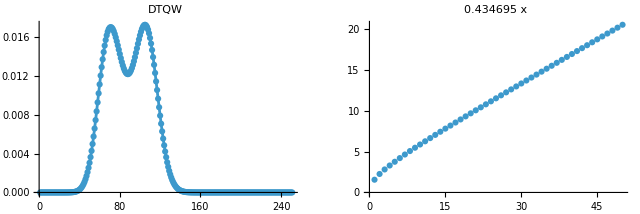

```mathematica
DTQWSummary[coin,50,envT4]
```

### 3 pasos

```mathematica
envT5=DTQWEnv[<|
"Type"->(ToString[#]<>"Ahead"),"Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->N[{0.5}~Join~ConstantArray[1/(2(#-1)),#-1]],
"Kraus"->(PermutationOperators/@Range[0,#-1])
|>]&@4;
```

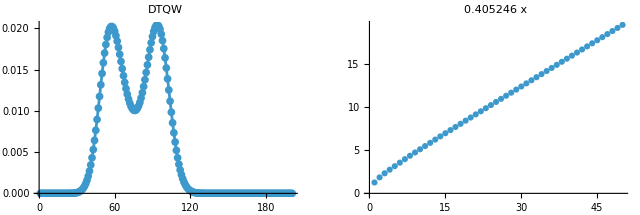

```mathematica
DTQWSummary[coin,50,envT5]
```

### 2 pasos

```mathematica
envT6=DTQWEnv[<|
"Type"->(ToString[#]<>"Ahead"),"Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->N[{0.5}~Join~ConstantArray[1/(2(#-1)),#-1]],
"Kraus"->(PermutationOperators/@Range[0,#-1])
|>]&@3;
```

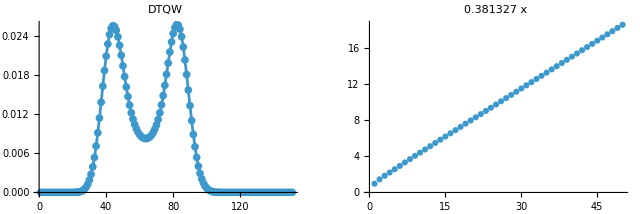

```mathematica
DTQWSummary[coin,50,envT6]
```

### 1 pasos

```mathematica
envT7=DTQWEnv[<|
"Type"->(ToString[#]<>"Ahead"),"Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->N[{0.5}~Join~ConstantArray[1/(2(#-1)),#-1]],
"Kraus"->(PermutationOperators/@Range[0,#-1])
|>]&@2;
```

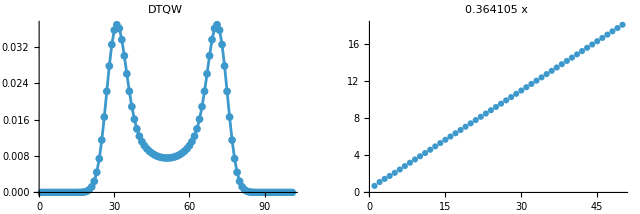

```mathematica
DTQWSummary[coin,50,envT7]
```

```mathematica
KroneckerProduct[{{x1,x2,x3}}ᵀ,{{c1,c2}}ᵀ]//MatrixForm
```

(c1 x1
c2 x1
c1 x2
c2 x2
c1 x3
c2 x3)

```mathematica
DTQWEquationPrint[{"p","q"},{"","K_1"}]
```

-Graphics-